```mathematica
TableForm[
Table[
With[
{row=Table[
StirlingS2[n,k],{k,1,n}]},
{n,First[First[Position[row,Max[row]]]],N[n/Log[n]],PrimePi[n]}
],
{n,1,50}
],
TableDepth->2
]
```

Power::infy: Infinite expression 1/0 encountered.

1 | 1 | ComplexInfinity | 0
2 | 1 | 2.88539 | 1
3 | 2 | 2.73072 | 2
4 | 2 | 2.88539 | 2
5 | 3 | 3.10667 | 3
6 | 3 | 3.34866 | 3
7 | 4 | 3.59729 | 4
8 | 4 | 3.84719 | 4
9 | 4 | 4.09608 | 4
10 | 5 | 4.34294 | 4
11 | 5 | 4.58736 | 5
12 | 5 | 4.82916 | 5
13 | 6 | 5.06833 | 6
14 | 6 | 5.30492 | 6
15 | 6 | 5.53904 | 6
16 | 7 | 5.77078 | 6
17 | 7 | 6.00025 | 7
18 | 7 | 6.22757 | 7
19 | 8 | 6.45284 | 8
20 | 8 | 6.67616 | 8
21 | 8 | 6.89763 | 8
22 | 9 | 7.11734 | 8
23 | 9 | 7.33537 | 9
24 | 9 | 7.55179 | 9
25 | 10 | 7.76669 | 9
26 | 10 | 7.98012 | 9
27 | 10 | 8.19215 | 9
28 | 10 | 8.40285 | 9
29 | 11 | 8.61225 | 10
30 | 11 | 8.82042 | 10
31 | 11 | 9.02741 | 11
32 | 12 | 9.23325 | 11
33 | 12 | 9.43799 | 11
34 | 12 | 9.64167 | 11
35 | 12 | 9.84432 | 11
36 | 13 | 10.046 | 11
37 | 13 | 10.2467 | 12
38 | 13 | 10.4465 | 12
39 | 14 | 10.6454 | 12
40 | 14 | 10.8434 | 12
41 | 14 | 11.0406 | 13
42 | 14 | 11.2369 | 13
43 | 15 | 11.4325 | 14
44 | 15 | 11.6273 | 14
45 | 15 | 11.8214 | 14
46 | 15 | 12.0147 | 14
47 | 16 | 12.2073 | 15
48 | 16 | 12.3993 | 15
49 | 16 | 12.5905 | 15
50 | 16 | 12.7811 | 15

```mathematica
Select[Table[
With[
{row=Table[
StirlingS2[n,k],{k,1,n}]},
{n,Length[Position[row,Max[row]]]}
],
{n,1,5000}
],#[[2]]≠1&]
```

{{2,2}}

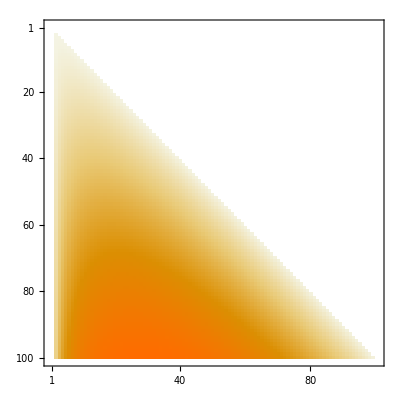

```mathematica
MatrixPlot[Table[
With[
{row=Table[
StirlingS2[n,k],{k,1,n}]},
PadRight[N[Log[row]],100]
],
{n,1,100}
]]
```

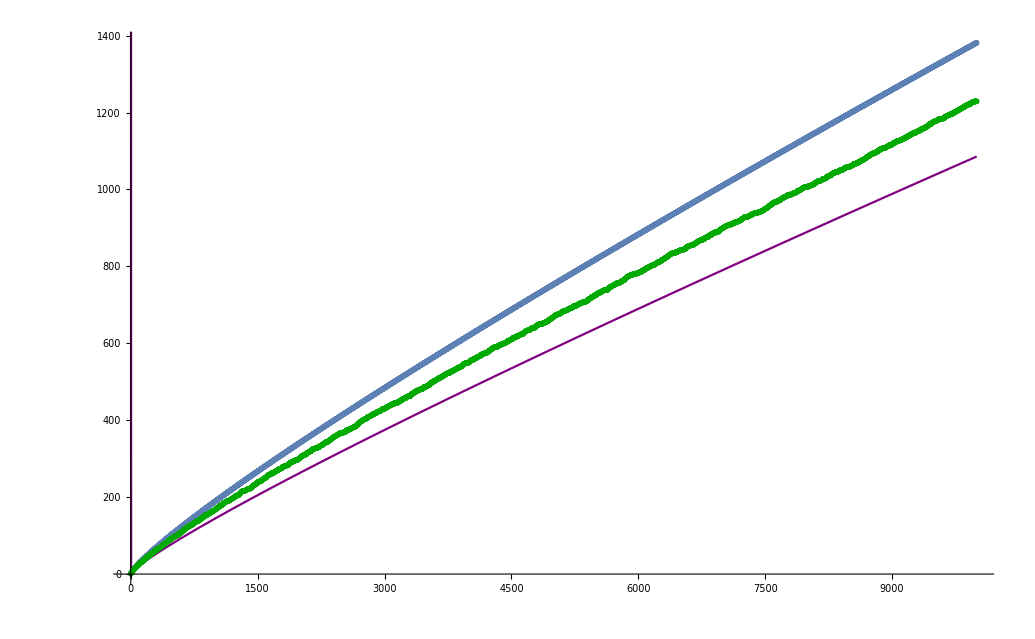

```mathematica
With[
{max=10000},
Show[
ListPlot[Table[
With[
{row=Table[
StirlingS2[n,k],{k,1,n}]},
{n,First[First[Position[row,Max[row]]]]}
],
{n,1,max}
]],
Plot[x/Log[x],{x,1,max},PlotStyle->Purple],
ListPlot[Table[{x,PrimePi[x]},{x,1,max}],PlotStyle->Darker[Green]]
]
]
```

Power::infy: Infinite expression 1/0 encountered.

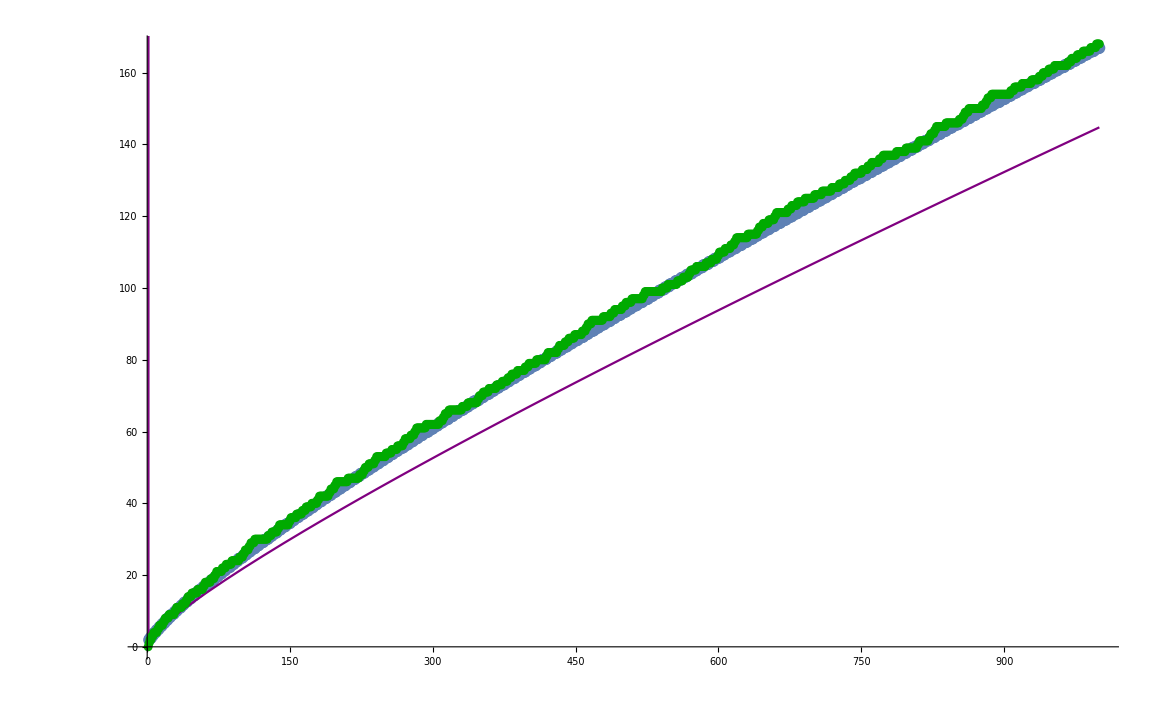

```mathematica
With[
{max=1000},
Show[
ListPlot[Table[
With[
{row=Table[
StirlingS2[n,k],{k,1,n}]},
{n,(First[First[Position[row,Max[row]]]]+n/Log[n])/2}
],
{n,1,max}
]],
Plot[x/Log[x],{x,1,max},PlotStyle->Purple],
ListPlot[Table[{x,PrimePi[x]},{x,1,max}],PlotStyle->Darker[Green]]
]
]
```